```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/poslavsky/Projects/redberry/bcbcnlo/src/check_ANDREI

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<renormAmpLarin.res
```

```mathematica
renormAmp/.X[1]->XX/.X[_]->0/.eps->Infinity
```

AL ((512 AS^2 pi AA(1) log(mmu/m^2) m^3)/(3 (1-4 r+6 r^2-4 r^3+r^4) s^4)-(1024 AS^2 pi AA(1) log(mmu/m^2) m^3)/(3 (1-3 r+3 r^2-r^3) s^4)+(512 AS^2 pi AA(1) log(mmu/m^2) m^3)/(3 (1-2 r+r^2) s^4)-(256 AS^2 pi AA(1) log(mmu/m^2) m^3)/(3 r^2 s^4)+(512 AS^2 pi AA(1) log(mmu/m^2) m^3)/(3 r^3 s^4)-(256 AS^2 pi AA(1) log(mmu/m^2) m^3)/(3 r^4 s^4)-(1024 AS^2 pi AA(1) log(1-r) m^3)/(9 (1-4 r+6 r^2-4 r^3+r^4) s^4)+(2048 AS^2 pi AA(1) log(1-r) m^3)/(9 (1-3 r+3 r^2-r^3) s^4)-(1024 AS^2 pi AA(1) log(1-r) m^3)/(9 (1-2 r+r^2) s^4)+(1024 AS^2 pi AA(1) log(1-r) m^3)/(9 r^2 s^4)-(2048 AS^2 pi AA(1) log(1-r) m^3)/(9 r^3 s^4)+(1024 AS^2 pi AA(1) log(1-r) m^3)/(9 r^4 s^4)-(2048 AS^2 pi AA(1) log(r) m^3)/(9 (1-4 r+6 r^2-4 r^3+r^4) s^4)+(4096 AS^2 pi AA(1) log(r) m^3)/(9 (1-3 r+3 r^2-r^3) s^4)-(2048 AS^2 pi AA(1) log(r) m^3)/(9 (1-2 r+r^2) s^4)+(512 AS^2 pi AA(1) log(r) m^3)/(9 r^2 s^4)-(1024 AS^2 pi AA(1) log(r) m^3)/(9 r^3 s^4)+(512 AS^2 pi AA(1) log(r) m^3)/(9 r^4 s^4)-(256 AS pi^2 AA(1) m)/(9 (1-3 r+3 r^2-r^3) s^3)+(32 AS^2 pi AA(1) m)/(9 r^2 s^3)+(128 AS pi^2 AA(1) m)/(9 r^3 s^3)-(32 AS^2 pi AA(1) m)/(9 r^3 s^3)+(4864 AS^2 pi AA(1) log(mmu/m^2) m)/(27 (1-3 r+3 r^2-r^3) s^3)+(128 AS^2 pi AA(1) log(mmu/m^2) m)/(3 (1-2 r+r^2) s^3)-(64 AS^2 pi AA(1) log(mmu/m^2) m)/(3 r^2 s^3)-(2432 AS^2 pi AA(1) log(mmu/m^2) m)/(27 r^3 s^3)-(5248 AS^2 pi AA(1) log(1-r) m)/(27 (1-3 r+3 r^2-r^3) s^3)-(256 AS^2 pi AA(1) log(1-r) m)/(9 (1-2 r+r^2) s^3)+(256 AS^2 pi AA(1) log(1-r) m)/(9 r^2 s^3)+(2240 AS^2 pi AA(1) log(1-r) m)/(27 r^3 s^3)-(4480 AS^2 pi AA(1) log(r) m)/(27 (1-3 r+3 r^2-r^3) s^3)-(512 AS^2 pi AA(1) log(r) m)/(9 (1-2 r+r^2) s^3)+(128 AS^2 pi AA(1) log(r) m)/(9 r^2 s^3)+(2624 AS^2 pi AA(1) log(r) m)/(27 r^3 s^3))

```mathematica
<<renormAmpSquaredCheckLarin.res
```

```mathematica
X[a_]:=norm
```

```mathematica
A1=Coefficient[renormAmp,AA[1]];
```

```mathematica
A1B1=Coefficient[matrixelement,AA[1] BB[1]];
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=15^2;mt=175;AL=1/137;
```

```mathematica
(2mc+2 mc)^2
```

36.

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[A1//N],{A[___],B[___],C[___]}]
```

0.000120416 log(0.234375) AS^2+0.000135292 log(0.765625) AS^2-0.000127854 log(0.0244141 mmu) AS^2-(0.0000601338 AS^2)/eps-2.72428×10^-6 AS^2+0.0000421487 AS+(3.34491×10^-6 AS^2 eps^3-8.17926×10^-6 AS^2 eps^2-3.82539×10^-6 AS^2 eps+9.94479×10^-6 AS^2-(2.93679×10^-7 AS^2)/eps) A(1.5)+(8.90336×10^-7 AS^2 eps^3-4.93573×10^-6 AS^2 eps^2-1.15646×10^-6 AS^2 eps+6.00113×10^-6 AS^2+(8.99017×10^-8 AS^2)/eps) A(4.9)+(0.0000932264 AS^2 eps^3-0.0000875534 AS^2 eps^2-0.00011335 AS^2 eps+0.000106452 AS^2) B(12.3596,0.,0.)+(-2.1307×10^-7 AS^2 eps^3+6.24185×10^-6 AS^2 eps^2-1.89215×10^-6 AS^2 eps-7.58918×10^-6 AS^2+(2.61556×10^-6 AS^2)/eps) B(12.3596,1.5,1.5)+(5.67981×10^-6 AS^2 eps^3+0.0000121567 AS^2 eps^2-6.90582×10^-6 AS^2 eps-0.0000147807 AS^2) B(12.3596,4.9,4.9)+(-2.12909×10^-6 AS^2 eps^3-7.21819×10^-6 AS^2 eps^2+5.35581×10^-6 AS^2 eps+8.77627×10^-6 AS^2-(3.36444×10^-6 AS^2)/eps) B(51.9348,1.5,4.9)+(0.0000104708 AS^2 eps^3-4.12168×10^-6 AS^2 eps^2-9.96386×10^-6 AS^2 eps+5.01136×10^-6 AS^2-(3.36444×10^-6 AS^2)/eps) B(51.9348,4.9,1.5)+(-0.0000400848 AS^2 eps^3-0.0000411274 AS^2 eps^2+0.0000487373 AS^2 eps+0.0000500049 AS^2) B(76.7444,0.,4.9)+(-0.000112577 AS^2 eps^3+0.000170962 AS^2 eps^2+0.000136877 AS^2 eps-0.000207865 AS^2) B(76.7444,4.9,0.)+(0.0000519977 AS^2 eps^3-9.16951×10^-6 AS^2 eps^2-0.0000632216 AS^2 eps+0.0000111488 AS^2) B(131.891,0.,0.)+(1.77712×10^-6 AS^2 eps^3-3.40582×10^-6 AS^2 eps^2-2.16072×10^-6 AS^2 eps+4.14098×10^-6 AS^2) B(131.891,1.5,1.5)+(-3.78538×10^-7 AS^2 eps^3-9.91155×10^-7 AS^2 eps^2-1.69097×10^-6 AS^2 eps+1.2051×10^-6 AS^2+(2.61556×10^-6 AS^2)/eps) B(131.891,4.9,4.9)+(-0.000112511 AS^2 eps^3+0.0000468201 AS^2 eps^2+0.000136797 AS^2 eps-0.0000569264 AS^2) B(174.516,0.,1.5)+(-0.0000184498 AS^2 eps^3+2.79182×10^-6 AS^2 eps^2+0.0000224323 AS^2 eps-3.39444×10^-6 AS^2) B(174.516,1.5,0.)+(0.0000764724 AS^2 eps^3-0.0000376443 AS^2 eps^2-0.0000929793 AS^2 eps+0.00004577 AS^2) B(225.,1.5,1.5)+(-0.0000331747 AS^2 eps^3+0.0000384792 AS^2 eps^2+0.0000403356 AS^2 eps-0.0000467851 AS^2) B(225.,4.9,4.9)+(-0.000113574 AS^2 eps^3+0.0000257454 AS^2 eps^2+0.000138089 AS^2 eps-0.0000313027 AS^2) C[2.25,12.3596,2.25,0,1.5,0]+(0.000635107 AS^2 eps^3-0.000521006 AS^2 eps^2-0.000772198 AS^2 eps+0.000633467 AS^2) C[2.25,76.7444,40.96,4.9,1.5,0]+(0.0000309613 AS^2 eps^3+0.0000205129 AS^2 eps^2-0.0000376445 AS^2 eps-0.0000249407 AS^2) C[2.25,76.7444,51.9348,4.9,1.5,0]+(-0.000387889 AS^2 eps^3+0.0000561899 AS^2 eps^2+0.000471616 AS^2 eps-0.0000683187 AS^2) C[2.25,131.891,174.516,0,1.5,0]+(0.00004511 AS^2 eps^3+0.0000763775 AS^2 eps^2-0.0000548472 AS^2 eps-0.000092864 AS^2) C[2.25,174.516,131.891,1.5,1.5,0]+(0.00142485 AS^2 eps^3-0.000571773 AS^2 eps^2-0.00173241 AS^2 eps+0.000695193 AS^2) C[2.25,174.516,225,1.5,1.5,0]+(-0.00112438 AS^2 eps^3+0.00141216 AS^2 eps^2+0.00136709 AS^2 eps-0.00171698 AS^2) C[24.01,12.3596,76.7444,0,4.9,0]+(-0.000141043 AS^2 eps^3-0.000150645 AS^2 eps^2+0.000171488 AS^2 eps+0.000183163 AS^2) C[24.01,76.7444,12.3596,4.9,4.9,0]+(0.000761573 AS^2 eps^3+0.00124215 AS^2 eps^2-0.000925962 AS^2 eps-0.00151027 AS^2) C[24.01,76.7444,225,4.9,4.9,0]+(-0.00121169 AS^2 eps^3+0.00122083 AS^2 eps^2+0.00147324 AS^2 eps-0.00148435 AS^2) C[24.01,131.891,24.01,0,4.9,0]+(0.0017461 AS^2 eps^3-0.00136775 AS^2 eps^2-0.002123 AS^2 eps+0.00166298 AS^2) C[24.01,174.516,40.96,1.5,4.9,0]+(-0.0000909569 AS^2 eps^3-9.80196×10^-6 AS^2 eps^2+0.00011059 AS^2 eps+0.0000119178 AS^2) C[24.01,174.516,51.9348,1.5,4.9,0]+(5.15101×10^-6 AS^2 eps^3+7.74391×10^-6 AS^2 eps^2-6.26288×10^-6 AS^2 eps-9.41547×10^-6 AS^2) C[51.9348,51.9348,225,1.5,1.5,4.9]+(-0.0000782324 AS^2 eps^3+5.88731×10^-6 AS^2 eps^2+0.0000951192 AS^2 eps-7.15811×10^-6 AS^2) C[76.7444,2.25,51.9348,1.5,4.9,0]+(-0.00133896 AS^2 eps^3+0.000539703 AS^2 eps^2+0.00162798 AS^2 eps-0.0006562 AS^2) C[76.7444,12.3596,24.01,0,4.9,0]+(0.0000574431 AS^2 eps^3-0.0000527733 AS^2 eps^2-0.0000698425 AS^2 eps+0.0000641646 AS^2) C[76.7444,24.01,12.3596,4.9,4.9,0]+(-0.00203805 AS^2 eps^3-0.000187668 AS^2 eps^2+0.00247797 AS^2 eps+0.000228177 AS^2) C[76.7444,24.01,225,4.9,4.9,0]+(-0.000101408 AS^2 eps^3+5.52888×10^-6 AS^2 eps^2+0.000123297 AS^2 eps-6.72231×10^-6 AS^2) C[174.516,2.25,131.891,1.5,1.5,0]+(-0.000038815 AS^2 eps^3-0.0000117746 AS^2 eps^2+0.0000471934 AS^2 eps+0.0000143162 AS^2) C[174.516,24.01,51.9348,4.9,1.5,0]+(-0.000813887 AS^2 eps^3+0.000355842 AS^2 eps^2+0.000989568 AS^2 eps-0.000432652 AS^2) C[174.516,131.891,2.25,0,1.5,0]+(-6.06144×10^-6 AS^2 eps^3+0.0000230495 AS^2 eps^2+7.36982×10^-6 AS^2 eps-0.0000280248 AS^2) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
B[14,0.,0.]/.{B[s_,0.,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]}
```

0.5 eps (-(1.27811-6.28319 ⅈ) log(mmu)-(5.46121+4.01532 ⅈ)+1. log^2(mmu))-(0.639057-3.14159 ⅈ)+1/eps+log(mmu)

```mathematica
ex[2]=Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],log[a_]:>  Log[a]},{eps,0,0}]]
```

-0.0000313027 AS^2 C[2.25,12.3596,2.25,0,1.5,0]+0.000633467 AS^2 C[2.25,76.7444,40.96,4.9,1.5,0]-0.0000249407 AS^2 C[2.25,76.7444,51.9348,4.9,1.5,0]-0.0000683187 AS^2 C[2.25,131.891,174.516,0,1.5,0]-0.000092864 AS^2 C[2.25,174.516,131.891,1.5,1.5,0]+0.000695193 AS^2 C[2.25,174.516,225,1.5,1.5,0]-0.00171698 AS^2 C[24.01,12.3596,76.7444,0,4.9,0]+0.000183163 AS^2 C[24.01,76.7444,12.3596,4.9,4.9,0]-0.00151027 AS^2 C[24.01,76.7444,225,4.9,4.9,0]-0.00148435 AS^2 C[24.01,131.891,24.01,0,4.9,0]+0.00166298 AS^2 C[24.01,174.516,40.96,1.5,4.9,0]+0.0000119178 AS^2 C[24.01,174.516,51.9348,1.5,4.9,0]-9.41547×10^-6 AS^2 C[51.9348,51.9348,225,1.5,1.5,4.9]-7.15811×10^-6 AS^2 C[76.7444,2.25,51.9348,1.5,4.9,0]-0.0006562 AS^2 C[76.7444,12.3596,24.01,0,4.9,0]+0.0000641646 AS^2 C[76.7444,24.01,12.3596,4.9,4.9,0]+0.000228177 AS^2 C[76.7444,24.01,225,4.9,4.9,0]-6.72231×10^-6 AS^2 C[174.516,2.25,131.891,1.5,1.5,0]+0.0000143162 AS^2 C[174.516,24.01,51.9348,4.9,1.5,0]-0.000432652 AS^2 C[174.516,131.891,2.25,0,1.5,0]-0.0000280248 AS^2 C[225,51.9348,51.9348,1.5,4.9,4.9]-(0.000101502+2.31045×10^-15 ⅈ) AS^2 log(mmu)+(0.000373752-0.000111271 ⅈ) AS^2+((3.81165×10^-21-3.04248×10^-31 ⅈ) AS^2)/eps^2+1/eps(2.15854×10^-6 AS^2 log(0.0416493 mmu)-6.60777×10^-7 AS^2 log(0.444444 mmu)-(1.49776×10^-6+3.04248×10^-31 ⅈ) AS^2 log(mmu)+(6.32501×10^-6-2.31045×10^-15 ⅈ) AS^2)+1.07927×10^-6 AS^2 log^2(0.0416493 mmu)-3.30389×10^-7 AS^2 log^2(0.444444 mmu)-(7.48881×10^-7+1.52124×10^-31 ⅈ) AS^2 log^2(mmu)-0.000127854 AS^2 log(0.0244141 mmu)+0.000146246 AS^2 log(0.0416493 mmu)+0.000021715 AS^2 log(0.444444 mmu)+0.0000421487 AS

```mathematica
(* ex[3]=LoopRefine[N[(Chop[ex[1]]/.{C[___]-> 0,B[s_,m1_,m2_]-> B[s+0.000000000000001*I,m1,m2],log[a_]:>  Log[a]})/.topvABC]]/.{ϵ-> eps,μR^2-> mmu} *)
```

```mathematica
ex[3]=LoopRefine[ex[2]/.topvABC]
```

AS (0.0000421487+AS ((0.000168936+0.0000486261 ⅈ)+(3.81165×10^-21-3.04248×10^-31 ⅈ)/eps^2+(6.32501×10^-6-2.31045×10^-15 ⅈ)/eps))+(AS^2 (0.000146246 eps+2.15854×10^-6) log(0.0416493 mmu))/eps+(AS^2 (0.000021715 eps-6.60777×10^-7) log(0.444444 mmu))/eps+(AS^2 ((-0.000101502-2.31045×10^-15 ⅈ) eps-(1.49776×10^-6+2.8966×10^-31 ⅈ)) log(mmu))/eps+1.07927×10^-6 AS^2 log^2(0.0416493 mmu)-3.30389×10^-7 AS^2 log^2(0.444444 mmu)-(7.48881×10^-7+1.52124×10^-31 ⅈ) AS^2 log^2(mmu)-0.000127854 AS^2 log(0.0244141 mmu)

```mathematica
ex[4]=Chop[Normal[Series[FullSimplify[ex[3]],{eps,0,0}]]]
```

(0.000171846+0.0000486261 ⅈ) AS^2-0.0000677201 AS^2 log(mmu)+0.0000421487 AS

```mathematica
ex[5]=Collect[Chop[ex[4]],AS]/.{AS-> z *0.3}//Expand
```

(0.0000154661+4.37635×10^-6 ⅈ) z^2-6.09481×10^-6 z^2 log(mmu)+0.0000126446 z

```mathematica
ex[6]=Normal[Series[(Conjugate[ex[5]] ex[5])/.{Conjugate[z]-> z,Conjugate[Log[mmu]]-> Log[mmu]},{z,0,3}]]
```

z^3 (3.91126×10^-10-1.54133×10^-10 log(mmu))+1.59886×10^-10 z^2

```mathematica
ratioAmp[mu2_]:=Abs[N[Coefficient[ex[5],z^2]/Coefficient[ex[5],z]/.{mmu-> mu2}]]
```

```mathematica
ratioAmpSquare[mu2_]:=Abs[N[Coefficient[ex[6],z^3]/Coefficient[ex[6],z^2]/.{mmu-> mu2}]]
```

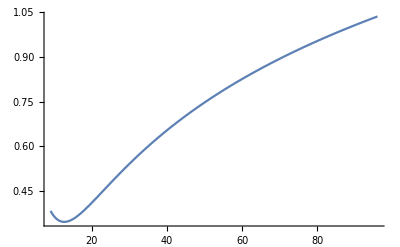

```mathematica
Plot[ratioAmp[mmu],{mmu,(2mc)^2,(2mb)^2}]
```

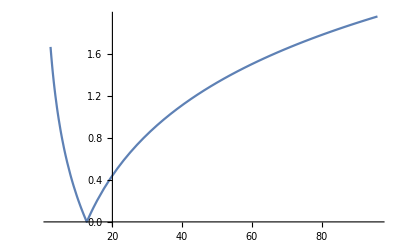

```mathematica
Plot[ratioAmpSquare[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioAmp[m^2]
```

0.663744

```mathematica
ratioAmp[(2mc)^2]
```

0.383017

```mathematica
ratioAmp[(mc)^2]
```

0.901359

```mathematica
ratioAmpSquare[(2mc)^2]
```

0.328113

```mathematica
ratioAmp[67]
```

0.874926

```mathematica
ratioAmpSquare[70]
```

1.64935

```mathematica
Sqrt[70]//N
```

8.3666

```mathematica
m
```

6.4

```mathematica
(MC=1.3,MB=4,MT=170,alphaS=0.3,alpha=1/137,fBc=1,mu=2*(MC+MB))
```

```mathematica
(* A[m_]:= A0[m]
B[s_,m1_,m2_]:= N[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]] *)
```

```mathematica
ex[7]=Collect[Expand[A1B1//N],{A[___],B[___],C[___],Aconj[___],Bconj[___],C[___]}]
```

4.78699×10^-9 eps^3 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-1.08514×10^-9 eps^2 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-5.82029×10^-9 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+1.31937×10^-9 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-2.6769×10^-8 eps^3 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+2.19597×10^-8 eps^2 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+3.25472×10^-8 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-2.66998×10^-8 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-1.30498×10^-9 eps^3 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-8.64592×10^-10 eps^2 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+1.58667×10^-9 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+1.05122×10^-9 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+1.6349×10^-8 eps^3 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-2.36833×10^-9 eps^2 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-1.9878×10^-8 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+2.87955×10^-9 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-1.90133×10^-9 eps^3 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-3.21922×10^-9 eps^2 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+2.31174×10^-9 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+3.9141×10^-9 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-6.00558×10^-8 eps^3 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+2.40995×10^-8 eps^2 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+7.30191×10^-8 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-2.93015×10^-8 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+4.73914×10^-8 eps^3 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-5.95208×10^-8 eps^2 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-5.7621×10^-8 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+7.23686×10^-8 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+5.9448×10^-9 eps^3 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+6.3495×10^-9 eps^2 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-7.228×10^-9 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-7.72007×10^-9 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-3.20994×10^-8 eps^3 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-5.23551×10^-8 eps^2 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+3.90281×10^-8 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+6.36561×10^-8 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+5.10713×10^-8 eps^3 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-5.14566×10^-8 eps^2 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-6.20952×10^-8 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+6.25637×10^-8 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-7.35959×10^-8 eps^3 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+5.76488×10^-8 eps^2 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+8.94819×10^-8 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-7.00925×10^-8 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+3.83372×10^-9 eps^3 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+4.1314×10^-10 eps^2 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-4.66124×10^-9 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-5.02318×10^-10 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-2.17109×10^-10 eps^3 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-3.26396×10^-10 eps^2 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+2.63972×10^-10 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+3.9685×10^-10 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+3.2974×10^-9 eps^3 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-2.48143×10^-10 eps^2 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-4.00916×10^-9 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+3.01705×10^-10 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+5.64355×10^-8 eps^3 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-2.27478×10^-8 eps^2 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-6.86173×10^-8 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+2.7658×10^-8 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-2.42116×10^-9 eps^3 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+2.22433×10^-9 eps^2 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+2.94377×10^-9 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-2.70446×10^-9 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+8.59013×10^-8 eps^3 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+7.90996×10^-9 eps^2 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-1.04443×10^-7 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-9.61735×10^-9 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+4.27422×10^-9 eps^3 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-2.33035×10^-10 eps^2 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-5.19683×10^-9 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+2.83337×10^-10 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+1.63601×10^-9 eps^3 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+4.96285×10^-10 eps^2 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-1.98914×10^-9 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-6.03411×10^-10 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+3.43043×10^-8 eps^3 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-1.49983×10^-8 eps^2 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-4.1709×10^-8 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+1.82357×10^-8 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+2.55482×10^-10 eps^3 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-9.71508×10^-10 eps^2 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-3.10629×10^-10 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+1.18121×10^-9 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-1.01508×10^-8 log(0.234375) AS^3-1.14047×10^-8 log(0.765625) AS^3+1.07778×10^-8 log(0.0244141 mmu) AS^3+(5.06913×10^-9 AS^3)/eps+2.2965×10^-10 AS^3-1.77652×10^-9 AS^2+(-1.40984×10^-10 eps^3 AS^3+3.44746×10^-10 eps^2 AS^3+1.61235×10^-10 eps AS^3+(1.23782×10^-11 AS^3)/eps-4.1916×10^-10 AS^3) A(1.5)+(-3.75265×10^-11 eps^3 AS^3+2.08035×10^-10 eps^2 AS^3+4.87433×10^-11 eps AS^3-(3.78924×10^-12 AS^3)/eps-2.5294×10^-10 AS^3) A(4.9)+(-1.40984×10^-10 eps^3 AS^3+3.44746×10^-10 eps^2 AS^3+1.61235×10^-10 eps AS^3+(1.23782×10^-11 AS^3)/eps-4.1916×10^-10 AS^3) Aconj(1.5)+(-3.75265×10^-11 eps^3 AS^3+2.08035×10^-10 eps^2 AS^3+4.87433×10^-11 eps AS^3-(3.78924×10^-12 AS^3)/eps-2.5294×10^-10 AS^3) Aconj(4.9)+(-3.92938×10^-9 eps^3 AS^3+3.69026×10^-9 eps^2 AS^3+4.77755×10^-9 eps AS^3-4.48682×10^-9 AS^3) B(12.3596,0.,0.)+(8.98062×10^-12 eps^3 AS^3-2.63086×10^-10 eps^2 AS^3+7.97518×10^-11 eps AS^3-(1.10243×10^-10 AS^3)/eps+3.19874×10^-10 AS^3) B(12.3596,1.5,1.5)+(-2.39397×10^-10 eps^3 AS^3-5.12389×10^-10 eps^2 AS^3+2.91072×10^-10 eps AS^3+6.2299×10^-10 AS^3) B(12.3596,4.9,4.9)+(8.97386×10^-11 eps^3 AS^3+3.04238×10^-10 eps^2 AS^3-2.25741×10^-10 eps AS^3+(1.41807×10^-10 AS^3)/eps-3.69909×10^-10 AS^3) B(51.9348,1.5,4.9)+(-4.41332×10^-10 eps^3 AS^3+1.73723×10^-10 eps^2 AS^3+4.19964×10^-10 eps AS^3+(1.41807×10^-10 AS^3)/eps-2.11222×10^-10 AS^3) B(51.9348,4.9,1.5)+(1.68952×10^-9 eps^3 AS^3+1.73347×10^-9 eps^2 AS^3-2.05421×10^-9 eps AS^3-2.10764×10^-9 AS^3) B(76.7444,0.,4.9)+(4.74498×10^-9 eps^3 AS^3-7.20584×10^-9 eps^2 AS^3-5.76921×10^-9 eps AS^3+8.76125×10^-9 AS^3) B(76.7444,4.9,0.)+(-2.19164×10^-9 eps^3 AS^3+3.86483×10^-10 eps^2 AS^3+2.66471×10^-9 eps AS^3-4.69907×10^-10 AS^3) B(131.891,0.,0.)+(-7.49033×10^-11 eps^3 AS^3+1.43551×10^-10 eps^2 AS^3+9.10715×10^-11 eps AS^3-1.74537×10^-10 AS^3) B(131.891,1.5,1.5)+(1.59549×10^-11 eps^3 AS^3+4.17759×10^-11 eps^2 AS^3+7.12721×10^-11 eps AS^3-(1.10243×10^-10 AS^3)/eps-5.07935×10^-11 AS^3) B(131.891,4.9,4.9)+(4.7422×10^-9 eps^3 AS^3-1.97341×10^-9 eps^2 AS^3-5.76582×10^-9 eps AS^3+2.39938×10^-9 AS^3) B(174.516,0.,1.5)+(7.77638×10^-10 eps^3 AS^3-1.17672×10^-10 eps^2 AS^3-9.45494×10^-10 eps AS^3+1.43071×10^-10 AS^3) B(174.516,1.5,0.)+(-3.22322×10^-9 eps^3 AS^3+1.58666×10^-9 eps^2 AS^3+3.91896×10^-9 eps AS^3-1.92915×10^-9 AS^3) B(225.,1.5,1.5)+(1.39827×10^-9 eps^3 AS^3-1.62185×10^-9 eps^2 AS^3-1.70009×10^-9 eps AS^3+1.97193×10^-9 AS^3) B(225.,4.9,4.9)+(-3.92938×10^-9 eps^3 AS^3+3.69026×10^-9 eps^2 AS^3+4.77755×10^-9 eps AS^3-4.48682×10^-9 AS^3) Bconj(12.3596,0.,0.)+(8.98062×10^-12 eps^3 AS^3-2.63086×10^-10 eps^2 AS^3+7.97518×10^-11 eps AS^3-(1.10243×10^-10 AS^3)/eps+3.19874×10^-10 AS^3) Bconj(12.3596,1.5,1.5)+(-2.39397×10^-10 eps^3 AS^3-5.12389×10^-10 eps^2 AS^3+2.91072×10^-10 eps AS^3+6.2299×10^-10 AS^3) Bconj(12.3596,4.9,4.9)+(8.97386×10^-11 eps^3 AS^3+3.04238×10^-10 eps^2 AS^3-2.25741×10^-10 eps AS^3+(1.41807×10^-10 AS^3)/eps-3.69909×10^-10 AS^3) Bconj(51.9348,1.5,4.9)+(-4.41332×10^-10 eps^3 AS^3+1.73723×10^-10 eps^2 AS^3+4.19964×10^-10 eps AS^3+(1.41807×10^-10 AS^3)/eps-2.11222×10^-10 AS^3) Bconj(51.9348,4.9,1.5)+(1.68952×10^-9 eps^3 AS^3+1.73347×10^-9 eps^2 AS^3-2.05421×10^-9 eps AS^3-2.10764×10^-9 AS^3) Bconj(76.7444,0.,4.9)+(4.74498×10^-9 eps^3 AS^3-7.20584×10^-9 eps^2 AS^3-5.76921×10^-9 eps AS^3+8.76125×10^-9 AS^3) Bconj(76.7444,4.9,0.)+(-2.19164×10^-9 eps^3 AS^3+3.86483×10^-10 eps^2 AS^3+2.66471×10^-9 eps AS^3-4.69907×10^-10 AS^3) Bconj(131.891,0.,0.)+(-7.49033×10^-11 eps^3 AS^3+1.43551×10^-10 eps^2 AS^3+9.10715×10^-11 eps AS^3-1.74537×10^-10 AS^3) Bconj(131.891,1.5,1.5)+(1.59549×10^-11 eps^3 AS^3+4.17759×10^-11 eps^2 AS^3+7.12721×10^-11 eps AS^3-(1.10243×10^-10 AS^3)/eps-5.07935×10^-11 AS^3) Bconj(131.891,4.9,4.9)+(4.7422×10^-9 eps^3 AS^3-1.97341×10^-9 eps^2 AS^3-5.76582×10^-9 eps AS^3+2.39938×10^-9 AS^3) Bconj(174.516,0.,1.5)+(7.77638×10^-10 eps^3 AS^3-1.17672×10^-10 eps^2 AS^3-9.45494×10^-10 eps AS^3+1.43071×10^-10 AS^3) Bconj(174.516,1.5,0.)+(-3.22322×10^-9 eps^3 AS^3+1.58666×10^-9 eps^2 AS^3+3.91896×10^-9 eps AS^3-1.92915×10^-9 AS^3) Bconj(225.,1.5,1.5)+(1.39827×10^-9 eps^3 AS^3-1.62185×10^-9 eps^2 AS^3-1.70009×10^-9 eps AS^3+1.97193×10^-9 AS^3) Bconj(225.,4.9,4.9)+(4.78699×10^-9 eps^3 AS^3-1.08514×10^-9 eps^2 AS^3-5.82029×10^-9 eps AS^3+1.31937×10^-9 AS^3) C[2.25,12.3596,2.25,0,1.5,0]+(-2.6769×10^-8 eps^3 AS^3+2.19597×10^-8 eps^2 AS^3+3.25472×10^-8 eps AS^3-2.66998×10^-8 AS^3) C[2.25,76.7444,40.96,4.9,1.5,0]+(-1.30498×10^-9 eps^3 AS^3-8.64592×10^-10 eps^2 AS^3+1.58667×10^-9 eps AS^3+1.05122×10^-9 AS^3) C[2.25,76.7444,51.9348,4.9,1.5,0]+(1.6349×10^-8 eps^3 AS^3-2.36833×10^-9 eps^2 AS^3-1.9878×10^-8 eps AS^3+2.87955×10^-9 AS^3) C[2.25,131.891,174.516,0,1.5,0]+(-1.90133×10^-9 eps^3 AS^3-3.21922×10^-9 eps^2 AS^3+2.31174×10^-9 eps AS^3+3.9141×10^-9 AS^3) C[2.25,174.516,131.891,1.5,1.5,0]+(-6.00558×10^-8 eps^3 AS^3+2.40995×10^-8 eps^2 AS^3+7.30191×10^-8 eps AS^3-2.93015×10^-8 AS^3) C[2.25,174.516,225,1.5,1.5,0]+(4.73914×10^-8 eps^3 AS^3-5.95208×10^-8 eps^2 AS^3-5.7621×10^-8 eps AS^3+7.23686×10^-8 AS^3) C[24.01,12.3596,76.7444,0,4.9,0]+(5.9448×10^-9 eps^3 AS^3+6.3495×10^-9 eps^2 AS^3-7.228×10^-9 eps AS^3-7.72007×10^-9 AS^3) C[24.01,76.7444,12.3596,4.9,4.9,0]+(-3.20994×10^-8 eps^3 AS^3-5.23551×10^-8 eps^2 AS^3+3.90281×10^-8 eps AS^3+6.36561×10^-8 AS^3) C[24.01,76.7444,225,4.9,4.9,0]+(5.10713×10^-8 eps^3 AS^3-5.14566×10^-8 eps^2 AS^3-6.20952×10^-8 eps AS^3+6.25637×10^-8 AS^3) C[24.01,131.891,24.01,0,4.9,0]+(-7.35959×10^-8 eps^3 AS^3+5.76488×10^-8 eps^2 AS^3+8.94819×10^-8 eps AS^3-7.00925×10^-8 AS^3) C[24.01,174.516,40.96,1.5,4.9,0]+(3.83372×10^-9 eps^3 AS^3+4.1314×10^-10 eps^2 AS^3-4.66124×10^-9 eps AS^3-5.02318×10^-10 AS^3) C[24.01,174.516,51.9348,1.5,4.9,0]+(-2.17109×10^-10 eps^3 AS^3-3.26396×10^-10 eps^2 AS^3+2.63972×10^-10 eps AS^3+3.9685×10^-10 AS^3) C[51.9348,51.9348,225,1.5,1.5,4.9]+(3.2974×10^-9 eps^3 AS^3-2.48143×10^-10 eps^2 AS^3-4.00916×10^-9 eps AS^3+3.01705×10^-10 AS^3) C[76.7444,2.25,51.9348,1.5,4.9,0]+(5.64355×10^-8 eps^3 AS^3-2.27478×10^-8 eps^2 AS^3-6.86173×10^-8 eps AS^3+2.7658×10^-8 AS^3) C[76.7444,12.3596,24.01,0,4.9,0]+(-2.42116×10^-9 eps^3 AS^3+2.22433×10^-9 eps^2 AS^3+2.94377×10^-9 eps AS^3-2.70446×10^-9 AS^3) C[76.7444,24.01,12.3596,4.9,4.9,0]+(8.59013×10^-8 eps^3 AS^3+7.90996×10^-9 eps^2 AS^3-1.04443×10^-7 eps AS^3-9.61735×10^-9 AS^3) C[76.7444,24.01,225,4.9,4.9,0]+(4.27422×10^-9 eps^3 AS^3-2.33035×10^-10 eps^2 AS^3-5.19683×10^-9 eps AS^3+2.83337×10^-10 AS^3) C[174.516,2.25,131.891,1.5,1.5,0]+(1.63601×10^-9 eps^3 AS^3+4.96285×10^-10 eps^2 AS^3-1.98914×10^-9 eps AS^3-6.03411×10^-10 AS^3) C[174.516,24.01,51.9348,4.9,1.5,0]+(3.43043×10^-8 eps^3 AS^3-1.49983×10^-8 eps^2 AS^3-4.1709×10^-8 eps AS^3+1.82357×10^-8 AS^3) C[174.516,131.891,2.25,0,1.5,0]+(2.55482×10^-10 eps^3 AS^3-9.71508×10^-10 eps^2 AS^3-3.10629×10^-10 eps AS^3+1.18121×10^-9 AS^3) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
ex[8]=Expand[Normal[Series[ex[7]/.{A[m_]:> A0[m],B[s_,0.,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> N[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[N[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[N[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[N[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[N[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]//.{Conjugate[eps]-> eps,mmu-> m^2}]
```

(1.66236×10^-8-9.69725×10^-9 ⅈ) eps^2 AS^3-(6.44466×10^-8+0. ⅈ) eps AS^3-5.82029×10^-9 eps C[2.25,12.3596,2.25,0,1.5,0] AS^3+1.31937×10^-9 C[2.25,12.3596,2.25,0,1.5,0] AS^3+3.25472×10^-8 eps C[2.25,76.7444,40.96,4.9,1.5,0] AS^3-2.66998×10^-8 C[2.25,76.7444,40.96,4.9,1.5,0] AS^3+1.58667×10^-9 eps C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3+1.05122×10^-9 C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3-1.9878×10^-8 eps C[2.25,131.891,174.516,0,1.5,0] AS^3+2.87955×10^-9 C[2.25,131.891,174.516,0,1.5,0] AS^3+2.31174×10^-9 eps C[2.25,174.516,131.891,1.5,1.5,0] AS^3+3.9141×10^-9 C[2.25,174.516,131.891,1.5,1.5,0] AS^3+7.30191×10^-8 eps C[2.25,174.516,225,1.5,1.5,0] AS^3-2.93015×10^-8 C[2.25,174.516,225,1.5,1.5,0] AS^3-5.7621×10^-8 eps C[24.01,12.3596,76.7444,0,4.9,0] AS^3+7.23686×10^-8 C[24.01,12.3596,76.7444,0,4.9,0] AS^3-7.228×10^-9 eps C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3-7.72007×10^-9 C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+3.90281×10^-8 eps C[24.01,76.7444,225,4.9,4.9,0] AS^3+6.36561×10^-8 C[24.01,76.7444,225,4.9,4.9,0] AS^3-6.20952×10^-8 eps C[24.01,131.891,24.01,0,4.9,0] AS^3+6.25637×10^-8 C[24.01,131.891,24.01,0,4.9,0] AS^3+8.94819×10^-8 eps C[24.01,174.516,40.96,1.5,4.9,0] AS^3-7.00925×10^-8 C[24.01,174.516,40.96,1.5,4.9,0] AS^3-4.66124×10^-9 eps C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-5.02318×10^-10 C[24.01,174.516,51.9348,1.5,4.9,0] AS^3+2.63972×10^-10 eps C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3+3.9685×10^-10 C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-4.00916×10^-9 eps C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3+3.01705×10^-10 C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3-6.86173×10^-8 eps C[76.7444,12.3596,24.01,0,4.9,0] AS^3+2.7658×10^-8 C[76.7444,12.3596,24.01,0,4.9,0] AS^3+2.94377×10^-9 eps C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3-2.70446×10^-9 C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3-1.04443×10^-7 eps C[76.7444,24.01,225,4.9,4.9,0] AS^3-9.61735×10^-9 C[76.7444,24.01,225,4.9,4.9,0] AS^3-5.19683×10^-9 eps C[174.516,2.25,131.891,1.5,1.5,0] AS^3+2.83337×10^-10 C[174.516,2.25,131.891,1.5,1.5,0] AS^3-1.98914×10^-9 eps C[174.516,24.01,51.9348,4.9,1.5,0] AS^3-6.03411×10^-10 C[174.516,24.01,51.9348,4.9,1.5,0] AS^3-4.1709×10^-8 eps C[174.516,131.891,2.25,0,1.5,0] AS^3+1.82357×10^-8 C[174.516,131.891,2.25,0,1.5,0] AS^3-3.10629×10^-10 eps C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+1.18121×10^-9 C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3-5.82029×10^-9 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+1.31937×10^-9 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3+3.25472×10^-8 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-2.66998×10^-8 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+1.58667×10^-9 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+1.05122×10^-9 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-1.9878×10^-8 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+2.87955×10^-9 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3+2.31174×10^-9 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+3.9141×10^-9 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3+7.30191×10^-8 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-2.93015×10^-8 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3-5.7621×10^-8 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+7.23686×10^-8 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-7.228×10^-9 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-7.72007×10^-9 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+3.90281×10^-8 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+6.36561×10^-8 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-6.20952×10^-8 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+6.25637×10^-8 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+8.94819×10^-8 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-7.00925×10^-8 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-4.66124×10^-9 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-5.02318×10^-10 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+2.63972×10^-10 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+3.9685×10^-10 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-4.00916×10^-9 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+3.01705×10^-10 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-6.86173×10^-8 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+2.7658×10^-8 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3+2.94377×10^-9 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-2.70446×10^-9 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-1.04443×10^-7 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-9.61735×10^-9 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-5.19683×10^-9 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+2.83337×10^-10 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-1.98914×10^-9 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-6.03411×10^-10 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-4.1709×10^-8 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+1.82357×10^-8 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-3.10629×10^-10 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+1.18121×10^-9 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+((1.48649×10^-19-5.62736×10^-27 ⅈ) AS^3)/eps+((3.10193×10^-25+0. ⅈ) AS^3)/eps^2-(1.05577×10^-8-1.13737×10^-24 ⅈ) AS^3-1.77652×10^-9 AS^2+0.

```mathematica
ex[9]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[8],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC]]]
```

6.70771×10^-9 AS^3-1.77652×10^-9 AS^2

```mathematica
ex[10]=Normal[Series[(Conjugate[ex[4]] ex[4])/.{Conjugate[AS]-> AS,Conjugate[Log[mmu]]-> Log[mmu]},{AS,0,3}]]/.{mmu-> m^2}
```

1.77652×10^-9 AS^2-6.70771×10^-9 AS^3

```mathematica
FullSimplify[Chop[FullSimplify[ex[9]/ex[10]]]]
```

-1.

```mathematica
ex[11]=Collect[Chop[ex[9]],AS]/.{AS-> z *0.3}//Expand
```

1.81108×10^-10 z^3-1.59886×10^-10 z^2

```mathematica
AmpSquareRatio=Abs[N[Coefficient[ex[11],z^3]/Coefficient[ex[11],z^2]]]
```

1.13273

```mathematica
ex[6]
```

z^3 (3.91126×10^-10-1.54133×10^-10 log(mmu))+1.59886×10^-10 z^2

```mathematica
AmpRatio=Abs[N[Coefficient[ex[6],z^3]/Coefficient[ex[6],z^2]]]/.{mmu-> m^2}
```

1.13273

```mathematica
LO2=+AL^2*(-16384/81*m^2*s^-6*r^-6*pi^4*AS^2-65536/81/(1-6*r+15*r^2-20*r^3+15*r^4-6*r^5+r^6)*m^2*s^-6*pi^4*AS^2+65536/81/(1-3*r+3*r^2-r^3)*m^2*s^-6*r^-3*pi^4*AS^2)
```

-1.77652×10^-9 AS^2

```mathematica
FullSimplify[AS^2 Coefficient[A1B1,AS^2]/LO2]
```

1.